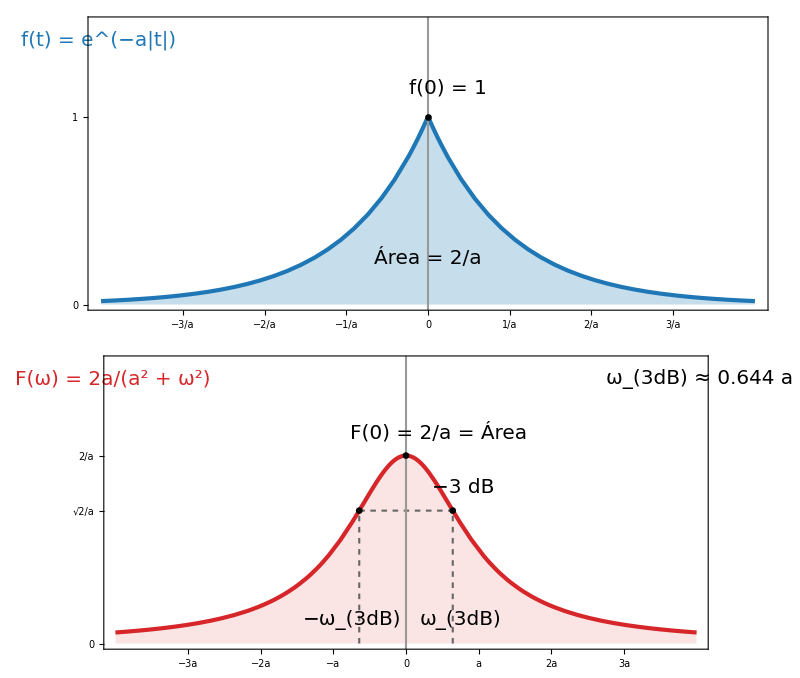

```mathematica
ClearAll[fs, aa, w3, blue, red, ft, Fw, tL, wL, ticksT, ticksW, tyT, tyF, label, g1, g2, fig];

fs = 20;                        (* tamaño de fuente único *)
aa = 1;                         (* parámetro a *)
w3 = aa Sqrt[Sqrt[2] - 1];      (* ω3dB = a √(√2 − 1) *)

blue = RGBColor[0.12, 0.47, 0.71];
red = RGBColor[0.84, 0.15, 0.16];

ft[t_] := Exp[-aa Abs[t]];
Fw[w_] := 2 aa/(aa^2 + w^2);

(* Texto con tamaño fs; pos puede ser una lista o Scaled[...] *)
label[expr_, col_, pos_, off_List : {-1, 0}] := Text[Style[expr, fs, col], pos, off];

tL = {"−3/a", "−2/a", "−1/a", "0", "1/a", "2/a", "3/a"};
wL = {"−3a", "−2a", "−a", "0", "a", "2a", "3a"};
ticksT = Table[{(k - 4)/aa, Style[tL[[k]], fs]}, {k, 7}];
ticksW = Table[{(k - 4) aa, Style[wL[[k]], fs]}, {k, 7}];
tyT = {{0, Style["0", fs]}, {1, Style["1", fs]}};
tyF = {{0, Style["0", fs]}, {Sqrt[2]/aa, Style["√2/a", fs]}, {2/aa, Style["2/a", fs]}};

(* Panel 1: señal en el tiempo con el área sombreada *)
g1 = Plot[ft[t], {t, -4/aa, 4/aa},
  PlotRange -> {{-4/aa, 4/aa}, {0, 1.5}},
  PlotRangePadding -> None,
  PlotStyle -> Directive[blue, AbsoluteThickness[3]],
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.25, blue]],
  Background -> White,
  Frame -> True,
  FrameStyle -> Directive[Black, AbsoluteThickness[1.5]],
  FrameTicks -> {{tyT, None}, {ticksT, None}},
  GridLines -> {{0}, None},
  GridLinesStyle -> Directive[GrayLevel[0.6], AbsoluteThickness[1.5]],
  AspectRatio -> 0.4,
  ImagePadding -> {{75, 15}, {45, 10}},
  Epilog -> {
    label[Row[{"f(t) = ", Superscript["e", "−a|t|"]}], blue, Scaled[{0.015, 0.92}]],
    label["Área = 2/a", Black, {0, 0.25}, {0, 0}],
    label["f(0) = 1", Black, {0.25, 1.15}],
    {Black, PointSize[0.012], Point[{0, 1}]}}];

(* Panel 2: espectro con F(0) y el punto de −3 dB *)
g2 = Plot[Fw[w], {w, -4 aa, 4 aa},
  PlotRange -> {{-4 aa, 4 aa}, {0, 3}},
  PlotRangePadding -> None,
  PlotStyle -> Directive[red, AbsoluteThickness[3]],
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.12, red]],
  Background -> White,
  Frame -> True,
  FrameStyle -> Directive[Black, AbsoluteThickness[1.5]],
  FrameTicks -> {{tyF, None}, {ticksW, None}},
  GridLines -> {{0}, None},
  GridLinesStyle -> Directive[GrayLevel[0.6], AbsoluteThickness[1.5]],
  AspectRatio -> 0.4,
  ImagePadding -> {{75, 15}, {45, 10}},
  Epilog -> {
    label[Row[{"F(ω) = 2a/(", Superscript["a", 2], " + ", Superscript["ω", 2], ")"}],
     red, Scaled[{0.015, 0.92}]],
    label[Row[{Subscript["ω", "3dB"], " ≈ 0.644 a"}], Black, Scaled[{0.985, 0.92}], {1, 0}],
    label["F(0) = 2/a = Área", Black, {0.45, 2.25}],
    {GrayLevel[0.4], AbsoluteThickness[1.5], Dashing[{0.01, 0.01}],
     Line[{{-w3, Sqrt[2]/aa}, {w3, Sqrt[2]/aa}}],
     Line[{{w3, 0}, {w3, Sqrt[2]/aa}}],
     Line[{{-w3, 0}, {-w3, Sqrt[2]/aa}}]},
    {Black, PointSize[0.012],
     Point[{{0, 2/aa}, {w3, Sqrt[2]/aa}, {-w3, Sqrt[2]/aa}}]},
    label["−3 dB", Black, {w3 + 0.15, Sqrt[2]/aa + 0.25}],
    label[Row[{Subscript["ω", "3dB"]}], Black, {w3 + 0.1, 0.25}],
    label[Row[{"−", Subscript["ω", "3dB"]}], Black, {-w3 - 0.1, 0.25}, {1, 0}]}];

fig = GraphicsColumn[{g1, g2}, Spacings -> 0, Background -> White, ImageSize -> 800]
```

```mathematica
Export["T2_Transformada_P1.png", fig, ImageResolution -> 300]
```

T2_Transformada_P1.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_Transformada_P1.png"]]]
```